```mathematica
img1=Import["C:\\Users\\Tom\\Desktop\\Plant XCT data\\T1_500_500_300_8bit Stack\\T1_500_500_300_8bit0000.tif"]
```

-Graphics-

```mathematica
img1b=Binarize[img1,{0.2,0.4}];
img1c=Dilation[Opening[img1b,DiskMatrix[6]],DiskMatrix[1]];
img1d=ImageMultiply[img1,img1c]
```

-Graphics-

```mathematica
mat1=ImageData[img1d];
list1=Flatten[mat1];
list2=Sort[list1,Greater];
list3=Take[list2,First[Position[list2,0.]][[1]]-1];
```

```mathematica
Mean[list3]
StandardDeviation[list3]
```

0.307889

0.0476733

```mathematica
G[x_,μ_,σ_]:=PDF[NormalDistribution[μ,σ],x]/PDF[NormalDistribution[μ,σ],μ]
```

```mathematica
GraphicsRow[Plot[G[x,0.5,#],{x,0,1},PlotRange->{0,1},Ticks->False,ImageSize->Tiny]&/@{0.15,0.1,0.05,0.01}]
```

-Graphics-

```mathematica
img1e=ImageApply[G[#,Mean[list3],StandardDeviation[list3]]&,img1]
```

-Graphics-

```mathematica
MedianFilter[img1e,5]
```

-Graphics-

```mathematica
img1f=Opening[Binarize[MedianFilter[img1e,5],0.5],DiskMatrix[2]]
```

-Graphics-

```mathematica
img1g=ImageMultiply[img1,img1f]
```

-Graphics-

```mathematica
mat2=ImageData[img1g];
list1a=Flatten[mat2];
list2a=Sort[list1a,Greater];
list3a=Take[list2a,First[Position[list2a,0.]][[1]]-1];
```

```mathematica
Mean[list3a]
StandardDeviation[list3a]
```

0.318922

0.0330686

```mathematica
img2=Import["C:\\Users\\Tom\\Desktop\\Plant XCT data\\T1_500_500_300_8bit Stack\\T1_500_500_300_8bit0001.tif"]
```

-Graphics-

```mathematica
img2a=ImageMultiply[img2,Dilation[img1f,DiskMatrix[10]]]
```

-Graphics-

```mathematica
img2b=ImageApply[G[#,Mean[list3a],StandardDeviation[list3a]]&,img2a]
```

-Graphics-

```mathematica
img2c=Opening[Binarize[MedianFilter[img2b,5],0.5],DiskMatrix[2]]
```

-Graphics-

```mathematica
img2d=ImageMultiply[img2,img2c];
mat2a=ImageData[img2d];
list2a=Flatten[mat2a];
list2b=Sort[list2a,Greater];
list2c=Take[list2b,First[Position[list2b,0.]][[1]]-1];
Mean[list2c]
StandardDeviation[list2c]
```

0.319113

0.0254225

```mathematica
files=FileNames["*.tif",NotebookDirectory[]];
```

```mathematica
stack=Import[#]&/@files;
```

```mathematica
img2a=ImageMultiply[img2,Dilation[img1f,DiskMatrix[10]]]
```

-Graphics-

```mathematica
img2b=ImageApply[G[#,Mean[list3a],StandardDeviation[list3a]]&,img2a]
```

-Graphics-

```mathematica
img1f=Opening[Binarize[MedianFilter[img2b,5],0.5],DiskMatrix[2]]
```

-Graphics-

```mathematica
img1g=ImageMultiply[img1,img1f]
```

-Graphics-

```mathematica
mat2=ImageData[img1g];
list1a=Flatten[mat2];
list2a=Sort[list1a,Greater];
list3a=Take[list2a,First[Position[list2a,0.]][[1]]-1];
```

```mathematica
stack2[1]=img1f;
mean[1]=Mean[list3];
sd[1]=StandardDeviation[list3];
```

```mathematica
Do[stackimga[i]=ImageMultiply[stack[[i]],Dilation[stack2[i-1],DiskMatrix[10]]];
stackimgb[i]=ImageApply[G[#,mean[i-1],sd[i-1]]&,stackimga[i]];
stack2[i]=Opening[Binarize[MedianFilter[stackimgb[i],5],0.4],DiskMatrix[2]];
stackimgc[i]=ImageMultiply[stack[[i]],stack2[i]];
mat[i]=ImageData[stackimgc[i]];
lista[i]=Flatten[mat[i]];
listb[i]=Sort[lista[i],Greater];
listc[i]=Take[listb[i],First[Position[listb[i],0.]][[1]]-1];
mean[i]=Mean[listc[i]];
sd[i]=If[i==2,StandardDeviation[listc[i]],If[StandardDeviation[listc[i]]>0.018,If[StandardDeviation[listc[i]]<StandardDeviation[listc[3]],StandardDeviation[listc[i]],StandardDeviation[listc[3]]],0.018]];
PrintTemporary["Currently processing slice ",i]
,{i,2,Length[stack]}]
```

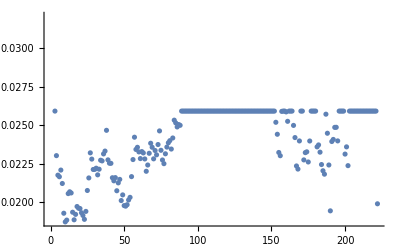

```mathematica
ListPlot[Table[sd[i],{i,1,226}]]
```

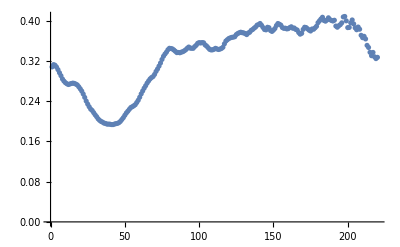

```mathematica
ListPlot[Table[mean[i],{i,1,220}]]
```

```mathematica
stack3=Table[stack2[i],{i,1,220}];
```

```mathematica
Image3D[stack3,ViewPoint->Front,Background->Brown]
```

-Graphics3D-

```mathematica
Image3D[stack3[[1;;220]],ViewPoint->Front,Background->Brown]
```

-Graphics3D-

```mathematica
meanmax=Max[Table[mean[i],{i,1,220}]]
```

0.408157

```mathematica
meanmin=Min[Table[mean[i],{i,1,220}]]
```

0.19329

```mathematica
Do[
stackimgb[i]=ImageApply[G[#,mean[i-1],sd[i-1]]&,stack[[i]]];
stack2[i]=Opening[Binarize[MedianFilter[stackimgb[i],5],0.5],DiskMatrix[2]];
stackimgc[i]=ImageMultiply[stack[[i]],stack2[i]];
mat[i]=ImageData[stackimgc[i]];
lista[i]=Flatten[mat[i]];
listb[i]=Sort[lista[i],Greater];
listc[i]=Take[listb[i],First[Position[listb[i],0.]][[1]]-1];
mean[i]=If[Mean[listc[i]]<meanmax,If[Mean[listc[i]]>meanmin,Mean[listc[i]],meanmin],meanmax];
sd[i]=If[i==2,StandardDeviation[listc[i]],If[StandardDeviation[listc[i]]>Mean[listc[i]]/10,If[StandardDeviation[listc[i]]<StandardDeviation[listc[3]],StandardDeviation[listc[i]],StandardDeviation[listc[3]]],Mean[listc[i]]/10]];
PrintTemporary["Currently processing slice ",i]
,{i,2,24}]
```

```mathematica
stack3=Table[stack2[i],{i,1,23}];
```

```mathematica
Image3D[stack3,ViewPoint->Front,Background->Brown]
```

-Graphics3D-

```mathematica
Image3DSlices[Image3D[stack3,ViewPoint->Front,Background->Brown]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NotebookSave[]
```